```mathematica
(Series[2^(-ϵ^2) ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify
```

(ⅇ^((-7+10 ϵ^2-42 ϵ^4+840 ϵ^6-2520 ⅈ ϵ^8 (π-ⅈ (3+Log[16])))/(10080 ϵ^6)) ϵ^(-1/12+ϵ^2/2))/Glaisher

```mathematica
PowerExpand@Log@(Series[ϵ^(-ϵ^2/2)ϵ^(1/12)ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify
```

1/12+1/(1008 ϵ^4)-1/(240 ϵ^2)-1/4 ⅈ (-3 ⅈ+π) ϵ^2-Log[Glaisher]

```mathematica
PowerExpand@Log@((Series[BarnesG[1+ ϵ ],{ϵ,Infinity,0}]//Normal)/.ϵ->I ϵ)
```

1/2 ⅈ ϵ (Log[2]+Log[π])+1/12 (1-(ⅈ π)/2-12 Log[Glaisher]-Log[ϵ])-1/4 ϵ^2 (-3+2 ((ⅈ π)/2+Log[ϵ]))

```mathematica
Simplify[Series[E^(2π I m ρ)r^(1/2(ν)(ν))E^(r( ν))((Series[BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)/.{ϵ->I ν}//Simplify)2^(ν^2)E^(I π ν^2/4)(1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11))/.{r-> t^1 ϵ^-1,ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,6}],{a>0,t>0,ϵ>0,ρ>0}]//Simplify
```

```mathematica
Series[Simplify[ϵ^(-ϵ^2/2)ϵ^(1/12)r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify/.{ϵ->I ν}) (1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)),{ν>0,ϵ>0,r>0}]/.{r-> t^1 ϵ^-1,ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,6}]
```

ⅇ^(-1/(1440 ϵ^6)+1/(1008 ϵ^4)+(-1+240 a t+15 t^2+240 a^2 Log[2]+120 a^2 Log[t/ϵ])/(240 ϵ^2)+1/12 (1-84 Log[2]-21 Log[t/ϵ])-1/4 ⅈ (-3 ⅈ+π) ϵ^2+O[ϵ]^6) ((4 a^6)/(Glaisher ϵ^6)-(16 (a^4-2 a^3 t))/(Glaisher ϵ^4)+(-11 a^2+16 a t+128 t^2)/(Glaisher ϵ^2)+O[ϵ]^7)

```mathematica
PowerExpand@Log@( ((Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify)/.ϵ->T)//Expand
```

1/12-1/(1440 T^6)+1/(1008 T^4)-1/(240 T^2)-(3 T^2)/4-1/4 ⅈ π T^2-Log[Glaisher]-Log[T]/12+1/2 T^2 Log[T]

```mathematica
Series[-ϵ^2PowerExpand[Series[Log[
t^(σ^2)( (Series[1/BarnesG[1+ϵ],{ϵ,Infinity,4}]//Normal)/.{ϵ->σ})( (Series[1/BarnesG[1+ϵ],{ϵ,Infinity,4}]//Normal)/.{ϵ-> -σ}) (1+t/(2 σ^2)+t^2(1-8 σ^2)/(4 σ^2(1-(2σ)^2)^2))],{t,0,4}]]/.{t-> t^1 ϵ^-4,σ ->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1}//Normal//Simplify,{ϵ,0,4}]
```

(ⅈ (3780 ⅈ a^6+1260 a^6 π-420 ⅈ a^4 ϵ^2-210 a^4 π ϵ^2+21 ⅈ a^2 ϵ^4-5 ⅈ ϵ^6+5040 ⅈ a^4 ϵ^2 Log[Glaisher]+2520 ⅈ a^6 Log[t/ϵ^4]-2520 ⅈ a^6 Log[a/ϵ]+420 ⅈ a^4 ϵ^2 Log[a/ϵ]))/(2520 a^4)-(ϵ^4 t)/(2 a^2 ϵ^4)+(ϵ^6 (32 a^4-10 a^2 ϵ^2+ϵ^4) (t/ϵ^4)^2)/(8 a^4 (4 a^2-ϵ^2)^2)-((ϵ^8 (40 a^4-11 a^2 ϵ^2+ϵ^4)) (t/ϵ^4)^3)/(24 (a^6 (4 a^2-ϵ^2)^2))+(ϵ^10 (896 a^8-608 a^6 ϵ^2+162 a^4 ϵ^4-20 a^2 ϵ^6+ϵ^8) (t/ϵ^4)^4)/(64 a^8 (4 a^2-ϵ^2)^4)+O[t/ϵ^4]^5

```mathematica
Series[(-ϵ^2Series[Log[1+t/(2 σ^2)+t^2(8 σ^2+1)/(4 σ^2(1-(2σ)^2)^2)]+Log[t^(σ^2)( (Series[1/BarnesG[1+ϵ],{ϵ,Infinity,4}]//Normal)/.{ϵ->2σ})( (Series[1/BarnesG[1+ϵ],{ϵ,Infinity,4}]//Normal)/.{ϵ-> -2σ}) ]//PowerExpand,{t,0,2}]//Normal)/.{t-> Λ^1 ϵ^-2,σ ->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,4}]
```

ⅈ (6 ⅈ a^2+2 a^2 π-4 ⅈ a^2 Log[2]-4 ⅈ a^2 Log[a/ϵ]+ⅈ a^2 Log[Λ/ϵ^2])-(ⅈ (2 ⅈ a^2+a^2 π-6 ⅈ Λ-2 ⅈ a^2 Log[2]-24 ⅈ a^2 Log[Glaisher]-2 ⅈ a^2 Log[a/ϵ]) ϵ^2)/(12 a^2)+((-2 a^4-75 Λ^2) ϵ^4)/(960 a^6)+O[ϵ]^5

```mathematica
Series[(-ϵ^2Series[Log[1+t/(2 σ^2)+t^2(8 σ^2+1)/(4 σ^2(1-(2σ)^2)^2)],{t,0,2}]//Normal)/.{t-> t^1 ϵ^-4,σ ->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,4}]
```

(-t/(2 a^2)-(5 t^2)/(64 a^6))-(t^2 ϵ^2)/(32 a^8)-(11 t^2 ϵ^4)/(1024 a^10)+O[ϵ]^5

```mathematica
t/(2 σ^2)/.{t-> t^1 ϵ^-4,σ ->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1}
```

t/(2 a^2 ϵ^2)

```mathematica
PowerExpand@Log[Series[Simplify[
r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,2}]//Normal)//Simplify/.{ϵ->I ν}) (1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)),{ν>0,ϵ>0,r>0}]/.{r-> t^1 ϵ^1,ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,2}]]//Simplify
```

(-1/240+a^2 Log[2]+1/2 a^2 (Log[t]+Log[ϵ]))/ϵ^2+O[ϵ]^0

```mathematica
Series[(-ϵ^2Series[Log[1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)]+Log[r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,2}]//Normal)//Simplify/.{ϵ->I ν}) ]//PowerExpand,{t,0,2}]//Normal)/.{r-> Λ^1 ϵ^1,ν ->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,4}]
```

1/240 (1-240 a^2 Log[2]-120 a^2 Log[ϵ Λ])+1/12 (-1-12 a Λ+12 Log[Glaisher]+Log[ϵ]-12 Log[a^6/(32 ϵ^8 Λ^2)]-3 Log[ϵ Λ]) ϵ^2+(ⅈ (-64 ⅈ-12 ⅈ a^2+4 a^2 π+ⅈ a^2 Λ^2+8 ⅈ a^2 Log[ϵ]) ϵ^4)/(16 a^2)+O[ϵ]^5

```mathematica
2^(z^2)E^(I π z^2/4)(2π)^(-I z/2)/.z->ν
```

2^(-(ⅈ ν)/2+ν^2) ⅇ^(1/4 ⅈ π ν^2) π^(-(ⅈ ν)/2)

```mathematica
Series[(-ϵ^0Series[Log[1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)]+Log[r^(ν^2/2+1/4)E^(α r^2/16+β r ν)2^(-(ⅈ ν)/2+ν^2) ⅇ^(1/4 ⅈ π ν^2) π^(-(ⅈ ν)/2)((Series[BarnesG[1+ x],{x,Infinity,2}]//Normal)/.x->I ν )]//PowerExpand,{t,0,2}]//Normal)/.{r-> 1^1 ϵ^-1,ν ->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,0}]//Simplify
```

(-12 a^2-α-16 a β-16 a^2 Log[2]-8 a^2 Log[1/ϵ]+8 a^2 Log[a/ϵ])/(16 ϵ^2)+1/24 (-2+ⅈ π+24 Log[Glaisher]-24 Log[a^6/(32 ϵ^4)]-6 Log[1/ϵ]+2 Log[a/ϵ])+O[ϵ]^1

```mathematica
(-12 a^2-α-16 a β-16 a^2 Log[2]+8 a^2 Log[a])/16//Expand
```

-(3 a^2)/4-α/16-a β-a^2 Log[2]+1/2 a^2 Log[a]

```mathematica
-a^2 Log[2]+1/2 a^2 Log[a/ϵ]
```

```mathematica
1/4 (-3+2 Log[Subscript[T, 1]]-4 Log[2]) Subscript[T, 1]^2//Expand
```

-(3 T_1^2)/4-Log[2] T_1^2+1/2 Log[T_1] T_1^2

```mathematica
n=2;
Sum[Subscript[T, k]^2/2(Log[Subscript[T, k]/c[k]]-3/2)-Subscript[T, k] Sin[π k/n]/Sin[π/n]/.c[z_]->4 Sin[π k/n]^3/Sin[π/n]//Cancel,{k,1,n}]+Sum[If[i<j,Subscript[T, i] Subscript[T, j] Log[(Cos[π(i-j)/n]-1)/(Cos[π(i+j)/n]-1)]//Simplify,0],{i,1,n},{j,1,n}]
```

∞ Sign[T_2]^2-T_1+1/4 (-3+2 Log[T_1/4]) T_1^2

```mathematica
n=3;
WantedTerm=Sum[Subscript[T, k]^2/2(Log[Subscript[T, k]/c[k]]-3/2)-Subscript[T, k] Sin[π k/n]/Sin[π/n]/.c[z_]->4 Sin[π k/n]^3/Sin[π/n]//Cancel,{k,1,n-1}]+Sum[If[i<j,Subscript[T, i] Subscript[T, j] Log[(Cos[π(i-j)/n]-1)/(Cos[π(i+j)/n]-1)]//Simplify,0],{i,1,n-1},{j,1,n-1}]//Expand
```

-T_1-(3 T_1^2)/4+1/2 Log[T_1/3] T_1^2-T_2-Log[4] T_1 T_2-(3 T_2^2)/4+1/2 Log[T_2/3] T_2^2

```mathematica
GottenTerm=-α/16-β1 Subscript[T, 1]-(3 Subscript[T, 1]^2)/4-1/4 Log[9] Subscript[T, 1]^2-α1 Log[1/ϵ] Subscript[T, 1]^2+1/2 Log[Subscript[T, 1]/ϵ] Subscript[T, 1]^2-β2 Subscript[T, 2]-β12 Subscript[T, 1] Subscript[T, 2]-α12 Log[1/ϵ] Subscript[T, 1] Subscript[T, 2]-(3 Subscript[T, 2]^2)/4-1/4 Log[9] Subscript[T, 2]^2-α2 Log[1/ϵ] Subscript[T, 2]^2+1/2 Log[Subscript[T, 2]/ϵ] Subscript[T, 2]^2/.{β1->1,β2->1,α1->1/2,α2->1/2,α12->0,β12->Log[4]}
```

-α/16-T_1-(3 T_1^2)/4-1/4 Log[9] T_1^2-1/2 Log[1/ϵ] T_1^2+1/2 Log[T_1/ϵ] T_1^2-T_2-Log[4] T_1 T_2-(3 T_2^2)/4-1/4 Log[9] T_2^2-1/2 Log[1/ϵ] T_2^2+1/2 Log[T_2/ϵ] T_2^2

```mathematica
WantedTerm-GottenTerm//FullSimplify
```

1/16 (α+8 (Log[1/ϵ]+Log[T_1]-Log[T_1/ϵ]) T_1^2+8 (Log[1/ϵ]+Log[T_2]-Log[T_2/ϵ]) T_2^2)

```mathematica
-α/16-Subscript[T, 1]-(3 Subscript[T, 1]^2)/4+1/2 Log[Subscript[T, 1]/3] Subscript[T, 1]^2-Subscript[T, 2]-α12 Log[1/ϵ] Subscript[T, 1] Subscript[T, 2]-(3 Subscript[T, 2]^2)/4+1/2 Log[Subscript[T, 2]/3] Subscript[T, 2]^2
```

```mathematica
r^(α1 Subscript[ν, 1]^2+α2 Subscript[ν, 2]^2+α12 Subscript[ν, 1] Subscript[ν, 2]+1/4)E^(α r^2/16+β1 r Subscript[ν, 1]+β2 r Subscript[ν, 2]+  β12  Subscript[ν, 1] Subscript[ν, 2])3^(Subscript[ν, 1]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 1]^2) π^(-(ⅈ Subscript[ν, 1])/2)BarnesG[1+ I ν1] 3^(Subscript[ν, 2]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 2]^2) π^(-(ⅈ Subscript[ν, 2])/2)BarnesG[1+ I ν2]/.{β1->1,β2->1,α1->1/2,α2->1/2,α12->0,β12->Log[4]}//Simplify
```

3^(1/2 (ν_1^2+ν_2^2)) 4^(ν_1 ν_2) ⅇ^((r^2 α)/16+r ν_1+1/4 ⅈ π ν_1^2+r ν_2+1/4 ⅈ π ν_2^2) π^(-1/2 ⅈ (ν_1+ν_2)) r^(1/4 (1+2 ν_1^2+2 ν_2^2)) BarnesG[1+ⅈ ν1] BarnesG[1+ⅈ ν2]

```mathematica
ⅇ^((r^2 α)/16+r Subscript[ν, 1]+r Subscript[ν, 2])  r^(1/4 (1+2 Subscript[ν, 1]^2+2 Subscript[ν, 2]^2))
```

```mathematica
Coefficient[Series[(-ϵ^0Log[ ⅇ^((r^2 α)/16+r Subscript[ν, 1]+r Subscript[ν, 2])  r^(1/4 (1+2 Subscript[ν, 1]^2+2 Subscript[ν, 2]^2))]//PowerExpand//Normal)/.{r-> 1^1 ϵ^-1,Subscript[ν, 1] ->Subscript[T, 1] ϵ^-1,Subscript[ν, 2] ->Subscript[T, 2] ϵ^-1},{ϵ,0,0}]//Simplify,ϵ,-2]//Expand
```

-α/16-T_1-1/2 Log[1/ϵ] T_1^2-T_2-1/2 Log[1/ϵ] T_2^2

```mathematica
Coefficient[Series[(-ϵ^0Log[ ⅇ^((r^2 α)/16+2 r x1+1 r x2+0 r x3) r^(1/4) r^(1/4 ( x1^2+x2^2+x3^2+2x1 x3))]//PowerExpand//Normal)/.{r-> 1^1 ϵ^-1,x1 ->X1 ϵ^-1,x2 ->X2 ϵ^-1,x3 ->X3 ϵ^-1},{ϵ,0,0}]//Simplify,ϵ,-2]/.{X1->Y1, X2-> Y2-Y1,X3->Y2}//Expand
```

-Y1-Y2-α/16-1/2 Y1^2 Log[1/ϵ]-1/2 Y2^2 Log[1/ϵ]

```mathematica
n
```

```mathematica
n=3;
t[k_,l_]:=Log[Sin[π/(2 n)(k+l)]^2/Sin[π/(2 n)(k-l)]^2];
td[k_]:=Log[16 n Sin[π/n k]^3];
a[d_]:=I/(2π)aD[d]^2(-Log[(-I aD[d])/Λ]+1)+I/(2 π)Sum[If[k≠d,t[k,d]aD[k],td[k]aD[k]],{k,1,n-1}]
Exp[Sum[D[a[k],aD[l]]aD[k]aD[l],{k,1,n-1},{l,1,n-1}]]//Simplify
```

ⅇ^(-(ⅈ (-aD[1]^3-aD[2]^3-2 aD[1] aD[2] Log[4]-aD[1]^2 Log[18 √3]-aD[2]^2 Log[18 √3]+2 aD[1]^3 Log[-(ⅈ aD[1])/Λ]+2 aD[2]^3 Log[-(ⅈ aD[2])/Λ]))/(2 π))

```mathematica
Solve[-45/8==N2/2^3,N2]
```

{{N2→-45}}

```mathematica
244/9-3/3^3
```

27

```mathematica
Residue[((Series[Log[z-E^x+Sqrt[(z-E^x)^2-4 E^-x]]-Log[2],{z,Infinity,2}]//Normal)/.x->Log[x])x,{x,Infinity}]
```

0

```mathematica
((Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,1}]//Simplify)//Normal)
```

-ⅇ^x z^(1/3)-1/2 ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)+(-2-ⅇ^(3 x)/3) z-1/4 ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x)) z^(4/3)-Log[z]/3

```mathematica
((Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,1}]//Simplify)/.x->Log[x]//Normal)
```

-x z^(1/3)-((2+x^3) z^(2/3))/(2 x)+(-2-x^3/3) z-((6+12 x^3+x^6) z^(4/3))/(4 x^2)-Log[z]/3

```mathematica
Aperiod[z_]=Residue[((Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,3}]//Simplify)/.x->Log[x]//Normal)/x,{x,Infinity}]
```

1/3 (6 z+45 z^2+560 z^3+Log[z])

```mathematica
Ž
```

```mathematica
Residue[x (-(ⅇ^-x (2+ⅇ^(3 x)))/(2 z^2)-ⅇ^x/z+Log[z]),{x,Infinity}]
```

Residue[x (-(ⅇ^-x (2+ⅇ^(3 x)))/(2 z^2)-ⅇ^x/z+Log[z]),{x,∞}]

```mathematica
Solve[z == E^(-3e),e]
```

{{e→ConditionalExpression[1/3 (2 ⅈ π C[1]+Log[1/z]),C[1]∈ℤ]}}

```mathematica
Aperiod[z_]=3Residue[((Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,4}]//Simplify)/.x->Log[x]//Normal)/x,{x,0}]//Expand
```

-6 z-45 z^2-560 z^3-(17325 z^4)/2-Log[z]

```mathematica
Solve[1/3 (6 z+45 z^2+560 z^3+Log[z])==t,z]
```

Solve[1/3 (6 z+45 z^2+560 z^3+Log[z])==t,z]

```mathematica
Simplify[1/3 (6 z+45 z^2+560 z^3+Log[z])/.z-> E^(-3e),e>0]//Expand
```

-e+(560 ⅇ^(-9 e))/3+15 ⅇ^(-6 e)+2 ⅇ^(-3 e)

```mathematica
Solve[-4 y^-1+(z^(-1/3)-y)^2==0,y]//Simplify
```

{{y→((z^(1/3)+(-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))^2)/(3 z^(2/3) (-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))},{y→1/6 (4/z^(1/3)-(1+ⅈ √3)/((-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))+(ⅈ (ⅈ+√3) (-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))/z^(2/3))},{y→1/6 (4/z^(1/3)+(ⅈ (ⅈ+√3))/((-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))-((1+ⅈ √3) (-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))/z^(2/3))}}

```mathematica
PowerExpand@(Log[Series[1/6 (4/z^(1/3)-(1+ⅈ √3)/((-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))+(ⅈ (ⅈ+√3) (-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))/z^(2/3)),{z,0,4},Assumptions->z>0]])//Simplify
```

2/3 Log[8 z]+8 z+80 z^2+(3584 z^3)/3+O[z]^(7/2)

```mathematica
Log[Series[((z^(1/3)+(-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3))^2)/(3 z^(2/3) (-z+54 z^2+6 √3 √(z^3 (-1+27 z)))^(1/3)),{z,0,3},Assumptions->z>0]]//Simplify
```

-Log[z]/3+2 √z-4 z+(35 z^(3/2))/3-40 z^2+(3003 z^(5/2))/20-(1792 z^3)/3+O[z]^(7/2)

```mathematica
Series[x-Log[8]+2 (Log[z^(-1/3)-ⅇ^x+√(-4 ⅇ^-x+(z^(-1/3)-ⅇ^x)^2)]),{z,0,2}]//Simplify
```

(x-Log[2]-(2 Log[z])/3)-2 ⅇ^x z^(1/3)-ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)-2/3 (6+ⅇ^(3 x)) z-1/2 (ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x))) z^(4/3)-2/5 (ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x))) z^(5/3)-1/3 (ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x))) z^2-2/7 (ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x))) z^(7/3)+O[z]^(8/3)

```mathematica
Integrate[(x-Log[2]-(2 Log[z])/3)-2 ⅇ^x z^(1/3)-ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)-2/3 (6+ⅇ^(3 x)) z-1/2 (ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x))) z^(4/3)-2/5 (ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x))) z^(5/3)-1/3 (ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x))) z^2-2/7 (ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x))) z^(7/3)+O[z]^(8/3),{x,2/3 Log[8 z]+8 z+80 z^2+(3584 z^3)/3+O[z]^(7/2),-Log[z]/3+2 √z-4 z+(35 z^(3/2))/3-40 z^2+(3003 z^(5/2))/20-(1792 z^3)/3+O[z]^(7/2)}]//Expand
```

(-2889/800+1/2 Log[z] Log[4 z])+(-49/5-Log[4]-2 Log[z]) √z+(-12/5+Log[16]+8 Log[z]) z-7/6 (73+Log[1024]+10 Log[z]) z^(3/2)+(1469/6+20 Log[2]+70 Log[z]) z^2-13/600 (21797+6930 Log[2 z]) z^(5/2)+4/45 (38749-6720 Log[2]+6720 Log[z]) z^3+O[z]^(7/2)

```mathematica
Series[(-2889/800+1/2 Log[z] Log[4 z])+(-49/5-Log[4]-2 Log[z]) √z+(-12/5+Log[16]+8 Log[z]) z-7/6 (73+Log[1024]+10 Log[z]) z^(3/2)+(1469/6+20 Log[2]+70 Log[z]) z^2-13/600 (21797+6930 Log[2 z]) z^(5/2)+4/45 (38749-6720 Log[2]+6720 Log[z]) z^3+O[z]^(7/2),{z,0,3}]
```

1/800 (-2889+400 Log[z] Log[4 z])+1/5 (-49-5 Log[4]-10 Log[z]) √z+1/5 (-12+5 Log[16]+40 Log[z]) z-7/6 (73+Log[1024]+10 Log[z]) z^(3/2)+1/6 (1469+120 Log[2]+420 Log[z]) z^2-13/600 (21797+6930 Log[2 z]) z^(5/2)-4/45 (-38749+6720 Log[2]-6720 Log[z]) z^3+O[z]^(7/2)

```mathematica
Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,2}]
```

-Log[z]/3-ⅇ^x z^(1/3)-1/2 (ⅇ^-x (2+ⅇ^(3 x))) z^(2/3)+1/3 (-6-ⅇ^(3 x)) z-1/4 (ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x))) z^(4/3)-1/5 (ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x))) z^(5/3)-1/6 (ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x))) z^2-1/7 (ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x))) z^(7/3)+O[z]^(8/3)

```mathematica
Integrate[1/2 (ⅇ^-x (2+ⅇ^(3 x)))/x,{x,δ,L}]
```

$Aborted

```mathematica
Integrate[((Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,2}]//Simplify)/.x->Log[x]//Normal)/x,{x,δ,L}]//Expand
```

$Aborted

```mathematica
Series[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,10}],{z,0,3}]
```

Log[z]-6 z+45 z^2-560 z^3+O[z]^4

```mathematica
D[Log[z],{z,3}]//Simplify
```

2/z^3

```mathematica
D[Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,Infinity}],{z,3}]//Simplify
```

(2 (-1+HypergeometricPFQ[{1/3,2/3},{1},-27 z]+6 z HypergeometricPFQ[{4/3,5/3},{2},-27 z]+90 z^2 HypergeometricPFQ[{7/3,8/3},{3},-27 z]))/z^3

```mathematica
Series[D[-1140830253/512 ⅇ^(-8 t)+(64639725 ⅇ^(-7 t))/343-(102365 ⅇ^(-6 t))/6+(211878 ⅇ^(-5 t))/125-(12333 ⅇ^(-4 t))/64+(244 ⅇ^(-3 t))/9-(45 ⅇ^(-2 t))/8+3 ⅇ^-t+t^3/18,{t,3}]/.{t->-Log[z]-Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,20}]},{z,0,2}]
```

1/3-3 z+63 z^2+O[z]^3

```mathematica
(D[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,3}],{z,1}]^3)(1/3-3 z+63 z^2+O[z]^3)
```

1/(3 z^3)-9/z^2+243/z+O[z]^0

```mathematica
Series[D[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,20}],{z,1}]^3,{z,0,3}]
```

1/z^3-18/z^2+378/z-8496+198450 z-4752108 z^2+115795224 z^3+O[z]^4

```mathematica
(1/z^3-18/z^2+378/z)(1/3-3 z+63 z^2+O[z]^3)
```

1/(3 z^3)-9/z^2+243/z+O[z]^0

```mathematica
Series[D[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,20}],{z,1}]^3 D[-1140830253/512 ⅇ^(-8 t)+(64639725 ⅇ^(-7 t))/343-(102365 ⅇ^(-6 t))/6+(211878 ⅇ^(-5 t))/125-(12333 ⅇ^(-4 t))/64+(244 ⅇ^(-3 t))/9-(45 ⅇ^(-2 t))/8+3 ⅇ^-t+t^3/18,{t,3}]/.{t->-Log[z]-Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,20}]},{z,0,2}]
Series[1/(3 z^3(1+27z)),{z,0,2}]
```

1/(3 z^3)-9/z^2+243/z-6561+177147 z-4782969 z^2+O[z]^3

1/(3 z^3)-9/z^2+243/z-6561+177147 z-4782969 z^2+O[z]^3

```mathematica
Series[D[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,5}],{z,1}]^3 D[-1140830253/512 ⅇ^(-8 t)+(64639725 ⅇ^(-7 t))/343-(102365 ⅇ^(-6 t))/6+(211878 ⅇ^(-5 t))/125-(12333 ⅇ^(-4 t))/64+(244 ⅇ^(-3 t))/9-(45 ⅇ^(-2 t))/8+3 ⅇ^-t+t^3/18,{t,3}]/.{t->-Log[z]-Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,5}]},{z,Infinity,2}]
```

-1134 ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21)-9692493829488 ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21)+549179103600 ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21)-31308949440 ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21)+1800115488 ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21)-104781168 ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21)+6219072 ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21)-382320 ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) O[1/z]^3+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-494411596221625351392771648 z^12+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-6402385292836382343814320 z^10+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-3848005993078003777020000 z^11+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-1597061390078827483050240 z^12+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-42127024520315220260544 z^8+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-29769098475799952577000 z^9+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-20681153989385891601600 z^10+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-12613107710488887201600 z^11+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-5344860201740552420928 z^12+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-318604984538046159240 z^6+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-256367740223725237800 z^7+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-136079826716161278720 z^8+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-97578030334373210160 z^9+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-69213292344686009520 z^10+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-43575995828155190400 z^11+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-19502044034567814720 z^12+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-1190505525099441264 z^4+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-1123537475707384500 z^5+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-1029166231902631200 z^6+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-840329751760584624 z^7+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-455416212922824384 z^8+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-337114368668579040 z^9+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-252541811036314800 z^10+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-178590146836701600 z^12+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-5421348571923324 z^2+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-4158649453890600 z^3+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-3845602375312320 z^4+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-3682764326084760 z^5+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-3444294419765640 z^6+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-2903186637068256 z^7+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-1661698660628160 z^8+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-1381616265035160 z^10+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-17512183275120 z^2+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-13631344022448 z^3+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-12870016904304 z^4+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-12827753426250 z+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-12723281731440 z^5+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-12567359838600 z^6+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-11898305889624 z^8+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-58607747964 z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-52144597260 z^6+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-47093817312 z^3+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-46959438960 z^4+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-42047189100 z+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (-24433816050/z+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (-20534944554/z^2+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-213844860 z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-193007448 z^4+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-145265400 z+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (-80089884/z+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (-66332520/z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-595350 z^2+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (-276696/z+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (-221994/z^2+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (-810/z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (-3/z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (54/z+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (13176/z^2+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (17010/z+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (25488 z+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (3813804/z^2+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (4661874/z+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (8930250 z+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (14256324 z^3+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (1163515050/z^2+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (1392982920/z+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (2447483850 z+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (2895111720 z^3+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (3130629264 z^5+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (3478543056 z^2+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (431233835634/z+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (731316033000 z+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (763873540416 z^4+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (782168958900 z^5+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (793453618728 z^3+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (837823989240 z^7+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (1006867138824 z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (110779910708544 z^9+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (178474588344360 z^7+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (204429053374560 z^6+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (214366439335860 z^5+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (221103822399264 z^4+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (226397763707850 z+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (237086488974240 z^3+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (307174954290300 z^2+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (16836120735754320 z^11+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (20724243975527400 z^9+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (27030298212884736 z^8+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (48913935512244264 z^7+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (59172157064064240 z^6+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (64053380382238800 z^5+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (67454338233970800 z^4+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (73396245244241448 z^3+O[1/z]^3)+ⅇ^(-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+O[1/z]^21) (1300136268971187648 z^13+O[1/z]^3)+ⅇ^(-(1513512 z^5)/5+17325 z^4-1120 z^3+90 z^2-12 z+2 Log[z]+O[1/z]^21) (2678852202550524000 z^11+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (4108013459524054080 z^10+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (5679824465559542760 z^9+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (7823941973701628544 z^8+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (14615640988696329120 z^7+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (18052237420958853000 z^6+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (19829378028236302260 z^5+O[1/z]^3)+ⅇ^(-(2270268 z^5)/5+(51975 z^4)/2-1680 z^3+135 z^2-18 z+3 Log[z]+O[1/z]^21) (317233249628969786112 z^12+O[1/z]^3)+ⅇ^(-(3027024 z^5)/5+34650 z^4-2240 z^3+180 z^2-24 z+4 Log[z]+O[1/z]^21) (734184093645680277600 z^11+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (1189067863083384604320 z^10+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (1697149787643889840800 z^9+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (2386927654574946436800 z^8+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (4524649106110379331624 z^7+O[1/z]^3)+ⅇ^(-756756 z^5+(86625 z^4)/2-2800 z^3+225 z^2-30 z+5 Log[z]+O[1/z]^21) (91823424132359098827648 z^12+O[1/z]^3)+ⅇ^(-(4540536 z^5)/5+51975 z^4-3360 z^3+270 z^2-36 z+6 Log[z]+O[1/z]^21) (219376564571267511408000 z^11+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (362760738141985637454000 z^10+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (525396544396325545565160 z^9+O[1/z]^3)+ⅇ^(-(5297292 z^5)/5+(121275 z^4)/2-3920 z^3+315 z^2-42 z+7 Log[z]+O[1/z]^21) (28013483629607867496705600 z^12+O[1/z]^3)+ⅇ^(-(6054048 z^5)/5+69300 z^4-4480 z^3+360 z^2-48 z+8 Log[z]+O[1/z]^21) (67913680799673812004501600 z^11+O[1/z]^3)+(-144459585441243072 z^12+19843349648522400 z^11-1870680081750480 z^10+153512918337240 z^9-12308878967616 z^8+1322033987736 z^7-93091554360 z^6+5793844140 z^5-347847696 z^4+21445272 z^3-1584036 z^2+66150 z-2832+126/z-6/z^2+O[1/z]^3)

```mathematica
3 ((3j-1)!)/(j!)^3 j(-z)^(-1+j)
```

```mathematica
Series[HypergeometricPFQ[{1/3,2/3},{1},-27 z]^3/z^3(-1140830253/512 ⅇ^(-8 t)+(64639725 ⅇ^(-7 t))/343-(102365 ⅇ^(-6 t))/6+(211878 ⅇ^(-5 t))/125-(12333 ⅇ^(-4 t))/64+(244 ⅇ^(-3 t))/9-(45 ⅇ^(-2 t))/8+3 ⅇ^-t+t^3/18/.t),{z,-1/27,1}]//Simplify
```

(19683 (2 EulerGamma+Log[1+27 z]+PolyGamma[0,1/3]+PolyGamma[0,2/3])^3)/(Gamma[1/3]^3 Gamma[2/3]^3)+O[z+1/27]^1

```mathematica
647/3888*x+156493/629856
```

```mathematica
-16(4(-1/48*t^4-1/2*t)^3+27(1/864*t^6+1/24*t^3+1/4)^2)/.{t->-z^(-1/3)}//Simplify
```

-27+1/z

```mathematica
(2^8 3^3(-1/48*t^4-1/2*t)^3)/(4(-1/48*t^4-1/2*t)^3+27(1/864*t^6+1/24*t^3+1/4)^2)/.{t->-z^(-1/3)}//Simplify
```

```mathematica
Series[(-1+24 z)^3/(z^3 (-1+27 z)),{z,Infinity,1}]
```

512/z+O[1/z]^2

```mathematica
x^3+(-1/48*t^4-1/2*t)*x+(1/864*t^6+1/24*t^3+1/4)/.{t->-z^(-1/3)}//FullSimplify
```

```mathematica
Series[x^3+(x (-1+24 z))/(48 z^(4/3))+(1+36 z (-1+6 z))/(864 z^2),{z,Infinity,2}]
```

(1/4+x^3)+1/2 x (1/z)^(1/3)-1/(24 z)-1/48 x (1/z)^(4/3)+1/(864 z^2)+O[1/z]^(7/3)

```mathematica
(1+36 z (-1+6 z))/(864 z^2)//Together
```

(1-36 z+216 z^2)/(864 z^2)

```mathematica
HypergeometricPFQ[{1/3,2/3},{1},-27 z]^3/z^3/.z->-1/27
```

-∞

```mathematica
1/z^3-18/z^2+378/z//Simplify
```

(1-18 z+378 z^2)/z^3

```mathematica
Series[(2 (HypergeometricPFQ[{1/3,2/3},{1},-27 z]+6 z (HypergeometricPFQ[{4/3,5/3},{2},-27 z]+15 z HypergeometricPFQ[{7/3,8/3},{3},-27 z])))/z^3,{z,-1/27,1}]
```

(-40/(3 (Gamma[7/3] Gamma[8/3]) (z+1/27)^2)+1/O[z+1/27])+Floor[(π-Arg[1+27 z])/(2 π)] ((9720 ⅈ π)/(Gamma[1/3] Gamma[2/3])+(806760 ⅈ π (z+1/27))/(Gamma[1/3] Gamma[2/3])+O[z+1/27]^2)+Floor[(π-Arg[1+27 z])/(2 π)] ((17496 ⅈ π)/(Gamma[1/3] Gamma[2/3])+(1469664 ⅈ π (z+1/27))/(Gamma[1/3] Gamma[2/3])+O[z+1/27]^2)+Floor[(π-Arg[1+27 z])/(2 π)] ((78732 ⅈ π)/(Gamma[1/3] Gamma[2/3])+(6849684 ⅈ π (z+1/27))/(Gamma[1/3] Gamma[2/3])+O[z+1/27]^2)

```mathematica
Series[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,10}],{z,Infinity,3}]
```

555099679134 z^10-(75957810500 z^9)/3+(4732755885 z^8)/4-(399072960 z^7)/7+2858856 z^6-(756756 z^5)/5+(17325 z^4)/2-560 z^3+45 z^2-6 z+Log[z]+O[1/z]^4

```mathematica
Simplify[Series[Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,10}],{z,-1/27,10}],Im[z]==0]
```

(386769083050603/1067583647898180+ⅈ π-3 Log[3])-(39388253380141 (z+1/27))/847288609443+(2204597712449 (z+1/27)^2)/6973568802-(482344502083 (z+1/27)^3)/14348907+(42650600901757 (z+1/27)^4)/57395628-(21626819289331 (z+1/27)^5)/885735+(4276675760939 (z+1/27)^6)/13122-(33355727274637 (z+1/27)^7)/5103+618095946641/72 (z+1/27)^8-1078200353363 (z+1/27)^9-200340135303309/10 (z+1/27)^10+O[z+1/27]^11

```mathematica
PowerExpand@(Log[z]^2+2Log[z]Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,3}]+Sum[18 (-z)^j ((3j-1)!)/(j!)^3(PolyGamma[3j]-PolyGamma[j+1]),{j,1,3}])//Expand
```

-18 z+(423 z^2)/2-2972 z^3-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2

```mathematica
((-Log[2]+Log[2 ⅇ^-x z^(1/3)])+ⅇ^x z^(1/3)+1/2 ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)+1/3 (6+ⅇ^(3 x)) z+1/4 ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x)) z^(4/3)+1/5 ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x)) z^(5/3)+1/6 ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x)) z^2+1/7 ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x)) z^(7/3)+1/8 ⅇ^(-4 x) (70+560 ⅇ^(3 x)+420 ⅇ^(6 x)+56 ⅇ^(9 x)+ⅇ^(12 x)) z^(8/3)+1/9 ⅇ^(-3 x) (630+1680 ⅇ^(3 x)+756 ⅇ^(6 x)+72 ⅇ^(9 x)+ⅇ^(12 x)) z^3+O[z]^(10/3)//Normal)
```

ⅇ^x z^(1/3)+1/2 ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)+1/3 (6+ⅇ^(3 x)) z+1/4 ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x)) z^(4/3)+1/5 ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x)) z^(5/3)+1/6 ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x)) z^2+1/7 ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x)) z^(7/3)+1/8 ⅇ^(-4 x) (70+560 ⅇ^(3 x)+420 ⅇ^(6 x)+56 ⅇ^(9 x)+ⅇ^(12 x)) z^(8/3)+1/9 ⅇ^(-3 x) (630+1680 ⅇ^(3 x)+756 ⅇ^(6 x)+72 ⅇ^(9 x)+ⅇ^(12 x)) z^3-Log[2]+Log[2 ⅇ^-x z^(1/3)]

```mathematica
(3Residue[PowerExpand@((ⅇ^x z^(1/3)+1/2 ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)+1/3 (6+ⅇ^(3 x)) z+1/4 ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x)) z^(4/3)+1/5 ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x)) z^(5/3)+1/6 ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x)) z^2+1/7 ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x)) z^(7/3)+1/8 ⅇ^(-4 x) (70+560 ⅇ^(3 x)+420 ⅇ^(6 x)+56 ⅇ^(9 x)+ⅇ^(12 x)) z^(8/3)+1/9 ⅇ^(-3 x) (630+1680 ⅇ^(3 x)+756 ⅇ^(6 x)+72 ⅇ^(9 x)+ⅇ^(12 x)) z^3-Log[2]+Log[2]-0+1/3Log[ z])/.x->Log[x]//Simplify)/x//Expand,{x,0}]//Expand)//Expand
```

6 z+45 z^2+560 z^3+Log[z]

```mathematica
6 z+45 z^2+560 z^3
```

```mathematica
Series[Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[z^(-1/3)-E^x-Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]],{z,0,4}]
```

$Aborted

```mathematica
3/2 Residue[(Series[α-Log[8]+2 (Log[z^(-1/3)-ⅇ^x+√(-4 ⅇ^-x+(z^(-1/3)-ⅇ^x)^2)]),{z,0,4}]/.x->Log[x]//Normal)/x//Expand,{x,0}]//Expand
```

-6 z-45 z^2-560 z^3-(17325 z^4)/2+(3 α)/2+3 Log[2]-(3 Log[8])/2-Log[z]

```mathematica
Residue[-2 z^(1/3)-(2 z^(2/3))/x^2-x z^(2/3)-(4 z)/x-(2 x^2 z)/3-6 z^(4/3)-(3 z^(4/3))/x^3-1/2 x^3 z^(4/3)-(12 z^(5/3))/x^2-8 x z^(5/3)-2/5 x^4 z^(5/3)-(20 z^2)/(3 x^4)-(30 z^2)/x-10 x^2 z^2-(x^5 z^2)/3-60 z^(7/3)-(40 z^(7/3))/x^3-12 x^3 z^(7/3)-2/7 x^6 z^(7/3)-(35 z^(8/3))/(2 x^5)-(140 z^(8/3))/x^2-105 x z^(8/3)-14 x^4 z^(8/3)-1/4 x^7 z^(8/3)-(140 z^3)/x^4-(1120 z^3)/(3 x)-168 x^2 z^3-16 x^5 z^3-(2 x^8 z^3)/9-840 z^(10/3)-(252 z^(10/3))/(5 x^6)-(630 z^(10/3))/x^3-252 x^3 z^(10/3)-18 x^6 z^(10/3)-1/5 x^9 z^(10/3)-(504 z^(11/3))/x^5-(2100 z^(11/3))/x^2-1680 x z^(11/3)-360 x^4 z^(11/3)-20 x^7 z^(11/3)-2/11 x^10 z^(11/3)-(154 z^4)/x^7-(2772 z^4)/x^4-(5775 z^4)/x-3080 x^2 z^4-495 x^5 z^4-22 x^8 z^4-(x^11 z^4)/6-13860 z^(13/3)-(1848 z^(13/3))/x^6-(11088 z^(13/3))/x^3-5280 x^3 z^(13/3)-660 x^6 z^(13/3)-24 x^9 z^(13/3)-2/13 x^12 z^(13/3)+(2 Log[2])/x-Log[8]/x-(2 Log[z])/(3 x),{x,0}]
```

1/3 (-12 z-90 z^2-1120 z^3-17325 z^4+6 Log[2]-3 Log[8]-2 Log[z])

```mathematica
3Residue[((Series[Log[(z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x])/(z^(-1/3)-E^x-Sqrt[(z^(-1/3)-E^x)^2-4 E^-x])],{z,0,4}]//Simplify)/.x->Log[x]//Normal)/x,{x,0}]//Expand
```

$Aborted

```mathematica
Aperiod[z_]=-3Residue[((Series[Log[-z^(-1/3)-E^x+Sqrt[(-z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,4}]//Simplify)/.x->Log[x]//Normal)/x,{x,0}]//Expand
```

$Aborted

```mathematica
2e + x + 2(Log[1-E^(x-e)-Sqrt[(1-E^(x-e))^2-4 E^(-x-2e)]]-Log[2])
```

```mathematica
Series[x+Log[E^-x z^(-1/3)-1-E^-x Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2],{z,0,4},Assumptions->x>0]
```

$Aborted

```mathematica
3Residue[PowerExpand@(((-Log[2]+Log[2 ⅇ^-x z^(1/3)])+ⅇ^x z^(1/3)+1/2 ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)+1/3 (6+ⅇ^(3 x)) z+1/4 ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x)) z^(4/3)+1/5 ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x)) z^(5/3)+1/6 ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x)) z^2+1/7 ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x)) z^(7/3)+1/8 ⅇ^(-4 x) (70+560 ⅇ^(3 x)+420 ⅇ^(6 x)+56 ⅇ^(9 x)+ⅇ^(12 x)) z^(8/3)+1/9 ⅇ^(-3 x) (630+1680 ⅇ^(3 x)+756 ⅇ^(6 x)+72 ⅇ^(9 x)+ⅇ^(12 x)) z^3+O[z]^(10/3)//Normal)/.x->Log[x]//Simplify)/x//Expand,{x,0}]//Expand
```

3 Residue[z^(1/3)+z^(2/3)/x^2+1/2 x z^(2/3)+(2 z)/x+(x^2 z)/3+3 z^(4/3)+(3 z^(4/3))/(2 x^3)+1/4 x^3 z^(4/3)+(6 z^(5/3))/x^2+4 x z^(5/3)+1/5 x^4 z^(5/3)+(10 z^2)/(3 x^4)+(15 z^2)/x+5 x^2 z^2+(x^5 z^2)/6+30 z^(7/3)+(20 z^(7/3))/x^3+6 x^3 z^(7/3)+1/7 x^6 z^(7/3)+(35 z^(8/3))/(4 x^5)+(70 z^(8/3))/x^2+105/2 x z^(8/3)+7 x^4 z^(8/3)+1/8 x^7 z^(8/3)+(70 z^3)/x^4+(560 z^3)/(3 x)+84 x^2 z^3+8 x^5 z^3+(x^8 z^3)/9-Log[x]/x+Log[z]/(3 x),{x,0}]

```mathematica
3 Residue[z^(1/3)+z^(2/3)/x^2+1/2 x z^(2/3)+(2 z)/x+(x^2 z)/3+3 z^(4/3)+(3 z^(4/3))/(2 x^3)+1/4 x^3 z^(4/3)+(6 z^(5/3))/x^2+4 x z^(5/3)+1/5 x^4 z^(5/3)+(10 z^2)/(3 x^4)+(15 z^2)/x+5 x^2 z^2+(x^5 z^2)/6+30 z^(7/3)+(20 z^(7/3))/x^3+6 x^3 z^(7/3)+1/7 x^6 z^(7/3)+(35 z^(8/3))/(4 x^5)+(70 z^(8/3))/x^2+105/2 x z^(8/3)+7 x^4 z^(8/3)+1/8 x^7 z^(8/3)+(70 z^3)/x^4+(560 z^3)/(3 x)+84 x^2 z^3+8 x^5 z^3+(x^8 z^3)/9,{x,0}]
```

6 z+45 z^2+560 z^3

```mathematica
Residue[(((-Log[2]+Log[2 ⅇ^-x z^(1/3)])+ⅇ^x z^(1/3)+1/2 ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)+1/3 (6+ⅇ^(3 x)) z+1/4 ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x)) z^(4/3)+1/5 ⅇ^-x (30+20 ⅇ^(3 x)+ⅇ^(6 x)) z^(5/3)+1/6 ⅇ^(-3 x) (20+90 ⅇ^(3 x)+30 ⅇ^(6 x)+ⅇ^(9 x)) z^2+1/7 ⅇ^(-2 x) (140+210 ⅇ^(3 x)+42 ⅇ^(6 x)+ⅇ^(9 x)) z^(7/3)+1/8 ⅇ^(-4 x) (70+560 ⅇ^(3 x)+420 ⅇ^(6 x)+56 ⅇ^(9 x)+ⅇ^(12 x)) z^(8/3)+1/9 ⅇ^(-3 x) (630+1680 ⅇ^(3 x)+756 ⅇ^(6 x)+72 ⅇ^(9 x)+ⅇ^(12 x)) z^3+O[z]^(10/3)//Simplify)/.x->Log[x]//Normal)/x//Expand,{x,0}]//Expand
```

```mathematica
-3/2 Residue[(Series[α-Log[4]+2 (Log[z^(-1/3)-ⅇ^x+√(-4 ⅇ^-x+(z^(-1/3)-ⅇ^x)^2)]),{z,0,4}]/.x->Log[x]//Normal)/x//Expand,{x,0}]//Expand
```

6 z+45 z^2+560 z^3+(17325 z^4)/2-(3 α)/2-3 Log[2]+(3 Log[4])/2+Log[z]

```mathematica
PowerExpand@(Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,10}])
```

-6 z+45 z^2-560 z^3+(17325 z^4)/2-(756756 z^5)/5+2858856 z^6-(399072960 z^7)/7+(4732755885 z^8)/4-(75957810500 z^9)/3+555099679134 z^10+Log[z]

```mathematica
Solve[t==-6 z+45 z^2-560 z^3+Log[z],z]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[t==-6 z+45 z^2-560 z^3+Log[z],z]

```mathematica
Solve[t==-6 z+Log[z],z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→-1/6 ProductLog[-6 ⅇ^t]}}

```mathematica
ProductLog
```

```mathematica
ProductLog
```

```mathematica
(-6 z+45 z^2-560 z^3+Log[z])^2//Expand
```

36 z^2-540 z^3+8745 z^4-50400 z^5+313600 z^6-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2

```mathematica
Series[Log[z+ϵ],{z,0,4}]
```

Log[ϵ]+z/ϵ-z^2/(2 ϵ^2)+z^3/(3 ϵ^3)-z^4/(4 ϵ^4)+O[z]^5

```mathematica
Series[InverseSeries[Series[Series[Log[z+ϵ],{z,0,4}]-6 z+45 z^2-560 z^3,{z,0,4}]]//Normal,{ϵ,0,1}]
```

1/24 (24 z+12 z^2+4 z^3+z^4-24 Log[ϵ]-24 z Log[ϵ]-12 z^2 Log[ϵ]-4 z^3 Log[ϵ]+12 Log[ϵ]^2+12 z Log[ϵ]^2+6 z^2 Log[ϵ]^2-4 Log[ϵ]^3-4 z Log[ϵ]^3+Log[ϵ]^4) ϵ+O[ϵ]^2

```mathematica
PowerExpand@(Log[z]^2+2Log[z]Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,3}]+Sum[18 (-z)^j ((3j-1)!)/(j!)^3(PolyGamma[3j]-PolyGamma[j+1]),{j,1,3}])//Expand
```

-18 z+(423 z^2)/2-2972 z^3-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2

```mathematica
Series[Simplify[6D[t^3/18+3 E^-t-45/8 E^(-2t)+244/9 E^(-3t),t]/.{t->-(-6 z+45 z^2-560 z^3+Log[z])},z>0],{z,0,3}]//Normal//Expand
```

-18 z+(423 z^2)/2-2972 z^3-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2

```mathematica
Series[Simplify[6D[t^3/18+3 E^-t-45/8 E^(-2t)+244/9 E^(-3t),t]/.{t->-(+Log[z])},z>0],{z,0,3}]//Normal//Expand
```

-18 z+(135 z^2)/2-488 z^3+Log[z]^2

```mathematica
-18 z+(423 z^2)/2-2972 z^3-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2/.Log[z]->(t-(-6 z+45 z^2-560 z^3))//Expand
```

t^2-18 z+(351 z^2)/2-2432 z^3-8745 z^4+50400 z^5-313600 z^6

```mathematica
t = f1[z] = -6 z+45 z^2-560 z^3+Log[z]
z = f1^-1 [t]
d F / d t = f2[z] = -18 z+(423 z^2)/2-2972 z^3-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2
---> F[t]?
```

```mathematica
nN=8;
Series[(Series[Simplify[1/6 D[Subscript[c, 0] t^3+Sum[Subscript[c, k] E^(-k t),{k,0,nN}],t]/.{t->-(Log[z]+Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,nN}])},z>0],{z,0,nN}]-(PowerExpand@(Log[z]^2+2Log[z]Sum[3 ((3j-1)!)/(j!)^3(-z)^j,{j,1,nN}]+Sum[18 (-z)^j ((3j-1)!)/(j!)^3(PolyGamma[3j]-PolyGamma[j+1]),{j,1,nN}])//Expand)//Expand),{z,0,nN}]/.{Subscript[c, 0]-> 2,Subscript[c, 1]-> 18 6,Subscript[c, 2]->-3 135/2,Subscript[c, 3]->2 488,Subscript[c, 4]-> -3 36999/16,Subscript[c, 5]->6 1271268/(25 5),Subscript[c, 6]->-614190,Subscript[c, 7]->6/7 387838350/49 ,Subscript[c, 8]-> -3422490759/32 3/4}//Simplify
```

O[z]^9

```mathematica
Product[1-E^(μ -c n),{n,1,Infinity}]
```

QPochhammer[ⅇ^μ,ⅇ^-c]/(1-ⅇ^μ)

```mathematica
Integrate[(E^(2/3 z-ϵ z^2))/(1 + E^z)E^(I z/(2 π b^2)q),{z,-Infinity,Infinity}]
```

$Aborted

```mathematica
Integrate[E^(2/3 z)/(1 + E^z)E^(I z/(2 π b^2)q),{z,-Infinity,Infinity}]
```

ConditionalExpression[π Sec[1/6 (π+(3 ⅈ q)/b^2)],-(2 π)/3<Im[q/b^2]<(4 π)/3]

```mathematica
π Sec[1/6 (π+(3 ⅈ q)/b^2)]
```

```mathematica
Cos[I x]
```

Cosh[x]

```mathematica
Limit[E^(2/3 z)/(1 + E^z),z-> -Infinity]
```

0

```mathematica
((1+Cot[π/6-(ⅈ (q1-q2))/(4 b^2)]^2) Tan[(2 b^2 π-3 ⅈ q1+3 ⅈ q2)/(12 b^2)])/(8 b^2 π)//FullSimplify
```

((1+Cot[π/6-(ⅈ (q1-q2))/(4 b^2)]^2) Tan[(2 b^2 π-3 ⅈ q1+3 ⅈ q2)/(12 b^2)])/(8 b^2 π)

```mathematica
Integrate[1/(2 π b)^2 E^(2/3 z)/(1 + E^z)E^(I z/(2 π b^2)(q1-q2)),{z,-Infinity,Infinity}]
```

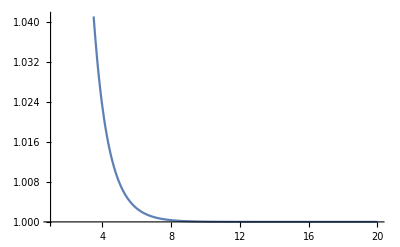

```mathematica
Plot[Sum[Exp[-l n^(1/2)],{n,0,100}],{l,1,20}]
```

```mathematica
Sum[Exp[-l n^(1/2)],{n,1,Infinity}]
```

∑_(n=1)^∞ ⅇ^(-l √n)

```mathematica
WolframAlpha["∑_(n = 1)^∞ ⅇ^(-l SqrtBox[n])"]
```

WolframAlphaQueryResults

```mathematica
1/(3 12)(Subscript[c, 0] t^3+Sum[Subscript[c, k] E^(-k t),{k,0,nN}]-2)/.{Subscript[c, 0]-> 2,Subscript[c, 1]-> 18 6,Subscript[c, 2]->-3 135/2,Subscript[c, 3]->2 488,Subscript[c, 4]-> -3 36999/16,Subscript[c, 5]->6 1271268/(25 5),Subscript[c, 6]->-614190,Subscript[c, 7]->6/7 387838350/49 ,Subscript[c, 8]-> -3422490759/32 3/4}//Simplify
```

-1140830253/512 ⅇ^(-8 t)+(64639725 ⅇ^(-7 t))/343-(102365 ⅇ^(-6 t))/6+(211878 ⅇ^(-5 t))/125-(12333 ⅇ^(-4 t))/64+(244 ⅇ^(-3 t))/9-(45 ⅇ^(-2 t))/8+3 ⅇ^-t+t^3/18

```mathematica
nN=4;
Series[(Series[Simplify[1/6 D[Subscript[c, 0] t^3+Sum[Subscript[c, k] E^(-k t),{k,0,nN}],t]/.{t->-(Log[z]+Sum[3 ((3j-1)!)/(j!)^3(z)^j,{j,1,nN}])},z>0],{z,0,nN}]-(PowerExpand@(Log[z]^2+2Log[z]Sum[3 ((3j-1)!)/(j!)^3(z)^j,{j,1,nN}]+Sum[18 (z)^j ((3j-1)!)/(j!)^3(PolyGamma[3j]-PolyGamma[j+1]),{j,1,nN}])//Expand)//Expand),{z,0,nN}]/.{Subscript[c, 0]-> 2,Subscript[c, 1]-> -18 6,Subscript[c, 2]->-3 135/2,Subscript[c, 3]->-2 488,Subscript[c, 4]-> -3 36999/16}//Simplify
```

O[z]^5

```mathematica
1/(3 12)(Subscript[c, 0] t^3+Sum[Subscript[c, k] E^(-k t),{k,0,nN}]-2)/.{Subscript[c, 0]-> 2,Subscript[c, 1]-> -18 6,Subscript[c, 2]->-3 135/2,Subscript[c, 3]->-2 488,Subscript[c, 4]-> -3 36999/16}//Simplify
```

-12333/64 ⅇ^(-4 t)-(244 ⅇ^(-3 t))/9-(45 ⅇ^(-2 t))/8-3 ⅇ^-t+t^3/18

```mathematica
Plot[]
```

```mathematica
Series[Simplify[6D[t^3/18+3 E^-t-45/8 E^(-2t)+244/9 E^(-3t),t]/.{t->-(-6 z+45 z^2-560 z^3+Log[z])},z>0],{z,0,3}]//Normal//Expand
```

-18 z+(423 z^2)/2-2972 z^3-12 z Log[z]+90 z^2 Log[z]-1120 z^3 Log[z]+Log[z]^2

```mathematica
PowerExpand@(Integrate[-z Log[z]^2-6 z^2 (-3-2 Log[z]+Log[z]^2)+9/2 z^3 (-23-4 Log[z]+12 Log[z]^2),z]/.z->E^(-3 t))
```

-369/16 ⅇ^(-12 t)+(38 ⅇ^(-9 t))/9-ⅇ^(-6 t)/4+135/4 ⅇ^(-12 t) t-16 ⅇ^(-9 t) t-3/2 ⅇ^(-6 t) t+243/2 ⅇ^(-12 t) t^2-18 ⅇ^(-9 t) t^2-9/2 ⅇ^(-6 t) t^2

```mathematica
1/6 Integrate[9 e^2-2972 ⅇ^(-9 e)+(423 ⅇ^(-6 e))/2-18 ⅇ^(-3 e)-6 e (-560 ⅇ^(-9 e)+45 ⅇ^(-6 e)-6 ⅇ^(-3 e))/.e->1/3 (-t),t]//Expand
```

-3 ⅇ^t+(333 ⅇ^(2 t))/8-(3898 ⅇ^(3 t))/9-6 ⅇ^t t+45/2 ⅇ^(2 t) t-560/3 ⅇ^(3 t) t+t^3/6

```mathematica
PowerExpand@Series[9 e^2+2972 ⅇ^(-9 e)+(423 ⅇ^(-6 e))/2+18 ⅇ^(-3 e)-6 e (560 ⅇ^(-9 e)+45 ⅇ^(-6 e)+6 ⅇ^(-3 e))/. e->1/3 (-t)//Simplify,{t,Infinity,1}]//Normal//Simplify
```

t^2+6 ⅇ^t (3+2 t)+9/2 ⅇ^(2 t) (47+20 t)+4 ⅇ^(3 t) (743+280 t)

```mathematica
∫(t^2+6 ⅇ^t (3+2 t)+9/2 ⅇ^(2 t) (47+20 t)+4 ⅇ^(3 t) (743+280 t))ⅆt//Expand
```

6 ⅇ^t+(333 ⅇ^(2 t))/4+(7796 ⅇ^(3 t))/9+12 ⅇ^t t+45 ⅇ^(2 t) t+1120/3 ⅇ^(3 t) t+t^3/3

```mathematica
∫(18 ⅇ^t+(423 ⅇ^(2 t))/2+2972 ⅇ^(3 t)+(6 ⅇ^t+45 ⅇ^(2 t)+560 ⅇ^(3 t)) t+t^2)ⅆt
```

t^3/3+6 ⅇ^t (2+t)+9/2 ⅇ^(2 t) (21+5 t)+4 ⅇ^(3 t) (2089/9+(140 t)/3)

```mathematica
Solve[t==-e+(560 ⅇ^(-9 e))/3+15 ⅇ^(-6 e)+2 ⅇ^(-3 e),e]
```

Solve[t==-e+(560 ⅇ^(-9 e))/3+15 ⅇ^(-6 e)+2 ⅇ^(-3 e),e]

```mathematica
Series[(E^e-E^x)^2-4 E^-x,{e,Infinity,1}]//Normal
```

ⅇ^(2 e)-4 ⅇ^-x+ⅇ^(2 x)-2 ⅇ^(e+x)

```mathematica
Series[ⅇ^(2 e)-4 ⅇ^-x+ⅇ^(2 x)-2 ⅇ^(e+x)/.x->-2e+2Log[2]//Simplify,{e,Infinity,1}]
```

16 ⅇ^(-4 e+O[1/e]^2)-8 ⅇ^(-e+O[1/e]^2)

```mathematica
Simplify[Log[z^(-1/3)-E^x-Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2]-(Log[z^(-1/3)-E^x+Sqrt[(z^(-1/3)-E^x)^2-4 E^-x]]-Log[2]),{x>0,z>0}]
```

-Log[4]+Log[-ⅇ^x-√(-4 ⅇ^-x+(ⅇ^x-1/z^(1/3))^2)+1/z^(1/3)]+Log[-ⅇ^x+√(-4 ⅇ^-x+(ⅇ^x-1/z^(1/3))^2)+1/z^(1/3)]

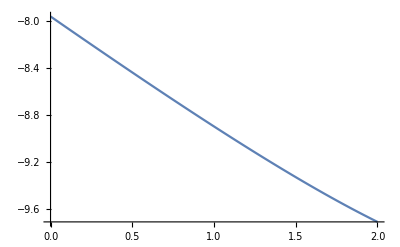

```mathematica
Plot[Log[E^e-E^x-Sqrt[(E^e-E^x)^2-4 E^-x]]-Log[2]-(Log[E^e-E^x+Sqrt[(E^e-E^x)^2-4 E^-x]]-Log[2])/.e->4,{x,0,2}]
```

```mathematica
PowerExpand@Log[(E^e-E^x+Sqrt[(E^e-E^x)^2-4 E^-x])/((E^e-E^x)^2-((E^e-E^x)^2-4 E^-x))(E^e-E^x+Sqrt[(E^e-E^x)^2-4 E^-x])/2]//Simplify
```

x-Log[8]+2 Log[ⅇ^e-ⅇ^x+√(-4 ⅇ^-x+(ⅇ^e-ⅇ^x)^2)]

```mathematica
Plot[2e + x + 2(Log[1-E^(x-e)-Sqrt[(1-E^(x-e))^2-4 E^(-x-2e)]]-Log[2])/.e->4,{x,0,2}]
```

-Graphics-

```mathematica
Integrate[x-Log[8]+2 (Log[ⅇ^e-ⅇ^x+√(-4 ⅇ^-x+(ⅇ^e-ⅇ^x)^2)]),{x,-2e+2Log[2] ,e},Assumptions->{e>0}]
```

$Aborted

```mathematica
Integrate[2 e + x,{x,-2e+2Log[2] ,e},Assumptions->{e>0}]//Simplify
```

(9 e^2)/2-2 Log[2]^2

```mathematica
Integrate[2Log[1-ⅇ^(x-e)],{x,0 ,e},Assumptions->{e>0}]//Expand
```

-π^2/3+2 PolyLog[2,ⅇ^-e]

```mathematica
Integrate[2Log[(1+√(1-4 ⅇ^(-x-2e)))/2],{x,-2e+2Log[2]  ,0 },Assumptions->{e>0}]//Simplify
```

ConditionalExpression[-π^2/6+2 Log[2]^2-Log[2/(1+√(1-4 ⅇ^(-2 e)))]^2+2 PolyLog[2,1/2 (1-√(1-4 ⅇ^(-2 e)))],e≥Log[2]]

```mathematica
PowerExpand@Series[(9 e^2)/2-2 Log[2]^2+(-π^2/3+2 PolyLog[2,ⅇ^-e])+(-π^2/6+2 Log[2]^2-Log[2/(1+√(1-4 ⅇ^(-2 e)))]^2+2 PolyLog[2,1/2 (1-√(1-4 ⅇ^(-2 e)))]),{e,Infinity,2}]//Normal//Simplify
```

1/36 (49+162 e^2+8 ⅇ^(-3 e)+72 ⅇ^-e-49 √(1-4 ⅇ^(-2 e))+4 ⅇ^(-2 e) (-3+√(1-4 ⅇ^(-2 e)))-18 π^2-36 Log[1/2 (1+√(1-4 ⅇ^(-2 e)))]^2)

```mathematica
1/36 (49+162 e^2+8 ⅇ^(-3 e)+72 ⅇ^-e-49 (1-2 ⅇ^(-2 e))+4 ⅇ^(-2 e) (-3+(1-2 ⅇ^(-2 e)))-18 π^2-36( ⅇ^(-2 e))^2)//Expand
```

(9 e^2)/2-(11 ⅇ^(-4 e))/9+(2 ⅇ^(-3 e))/9+(5 ⅇ^(-2 e))/2+2 ⅇ^-e-π^2/2

```mathematica
(9 e^2)/2-(11 ⅇ^(-4 e))/9+(2 ⅇ^(-3 e))/9+(5 ⅇ^(-2 e))/2+2 ⅇ^-e-π^2/2/.e->-3t
```

2 ⅇ^(3 t)+(5 ⅇ^(6 t))/2+(2 ⅇ^(9 t))/9-(11 ⅇ^(12 t))/9-π^2/2+(81 t^2)/2

```mathematica
9/2∫(2 ⅇ^(3 t)+(5 ⅇ^(6 t))/2+(2 ⅇ^(9 t))/9-(11 ⅇ^(12 t))/9-π^2/2+(81 t^2)/2)ⅆt//Expand
```

3 ⅇ^(3 t)+(15 ⅇ^(6 t))/8+ⅇ^(9 t)/9-(11 ⅇ^(12 t))/24-(9 π^2 t)/4+(243 t^3)/4

```mathematica
Series[Log[1/2 (1+√(1-4 z))],{z,0,1}]
```

-z+O[z]^2

```mathematica
Simplify[Series[1/36 (49+162 e^2+8 ⅇ^(-3 e)+72 ⅇ^-e-49 √(1-4 ⅇ^(-2 e))+4 ⅇ^(-2 e) (-3+√(1-4 ⅇ^(-2 e)))-18 π^2-36 Log[1/2 (1+√(1-4 ⅇ^(-2 e)))]^2)/.e->Log[z]//Simplify,{z,0,1}],z>0]//Simplify
```

(2/9+(2 ⅈ)/9)/z^3-1/(3 z^2)+(2-(11 ⅈ)/4)/z+(49/36-π^2/2-Log[ⅈ/z]^2+(9 Log[z]^2)/2)+ⅈ Log[ⅈ/z] z+O[z]^2

```mathematica
Integrate[x-Log[8],{x,-2e+2Log[2] ,e},Assumptions->{e>0}]//Simplify
```

-1/2 (3 e-Log[4]) (e+Log[16])

```mathematica
Series[2 (Log[z^(-1/3)-ⅇ^x+√(-4 ⅇ^-x+(z^(-1/3)-ⅇ^x)^2)]),{z,0,1}]//Simplify
```

(Log[4]-(2 Log[z])/3)-2 ⅇ^x z^(1/3)-ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)-2/3 (6+ⅇ^(3 x)) z-1/2 (ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x))) z^(4/3)+O[z]^(5/3)

```mathematica
Integrate[(Log[4]-(2 Log[z])/3)-2 ⅇ^x z^(1/3)-ⅇ^-x (2+ⅇ^(3 x)) z^(2/3)-2/3 (6+ⅇ^(3 x)) z-1/2 (ⅇ^(-2 x) (6+12 ⅇ^(3 x)+ⅇ^(6 x))) z^(4/3),{x,-2e+2Log[2] ,e},Assumptions->{e>0}]-1/2 (3 e-Log[4]) (e+Log[16])//Simplify
```

8 ⅇ^(-4 e) z^(2/3)+2 ⅇ^-e z^(2/3)-ⅇ^(2 e) z^(2/3)+128/9 ⅇ^(-6 e) z-2/9 ⅇ^(3 e) z+32 ⅇ^(-8 e) z^(4/3)-7/32 ⅇ^(4 e) z^(4/3)-2 ⅇ^e z^(1/3) (1+3 z)+1/2 ⅇ^(-2 e) z^(1/3) (16+51 z)+(3 e-Log[4]) (-4 z+Log[4])-1/2 (3 e-Log[4]) (e+Log[16])+2/3 (-3 e+Log[4]) Log[z]

```mathematica
Series[8 ⅇ^(-4 e) z^(2/3)+2 ⅇ^-e z^(2/3)-ⅇ^(2 e) z^(2/3)+128/9 ⅇ^(-6 e) z-2/9 ⅇ^(3 e) z+32 ⅇ^(-8 e) z^(4/3)-7/32 ⅇ^(4 e) z^(4/3)-2 ⅇ^e z^(1/3) (1+3 z)+1/2 ⅇ^(-2 e) z^(1/3) (16+51 z)+(3 e-Log[4]) (-4 z+Log[4])-1/2 (3 e-Log[4]) (e+Log[16])+2/3 (-3 e+Log[4]) Log[z]/.e->-1/3 Log[z],{z,0,2}]//Simplify
```

(-991/288-Log[4]^2+Log[2] Log[16]+Log[2] Log[z]+Log[z]^2/2)+(4+4 Log[4 z]) z+(67 z^2)/2+O[z]^3

```mathematica
Series[PowerExpand@Simplify[((-991/288-Log[4]^2+Log[2] Log[16]+Log[2] Log[z]+Log[z]^2/2)+(4+4 Log[4 z]) z+(67 z^2)/2+O[z]^3//Normal)/. z-> E^-t,t>0],{t,Infinity,1}]//Normal
```

-991/288+(67 ⅇ^(-2 t))/2+t^2/2-t Log[2]+ⅇ^-t (-4 t+4 (1+2 Log[2]))

```mathematica
1/3∫(-991/288+(67 ⅇ^(-2 t))/2+t^2/2-t Log[2]+ⅇ^-t (-4 t+4 (1+2 Log[2])))ⅆt//Expand
```

-67/12 ⅇ^(-2 t)-(991 t)/864+(4 ⅇ^-t t)/3+t^3/18-1/6 t^2 Log[2]-1/3 ⅇ^-t Log[256]

```mathematica
Log[256]/3//N
```

1.84839

```mathematica
∫(-991/288+(67 ⅇ^(-6 t))/2+(9 t^2)/2-3 t Log[2]+ⅇ^(-3 t) (-12 t+4 (1+2 Log[2])))ⅆt
```

-67/12 ⅇ^(-6 t)-(991 t)/288+(3 t^3)/2-1/2 t^2 Log[8]+1/3 ⅇ^(-3 t) (12 t-Log[256])

```mathematica
Integrate[(47 ⅇ^(-2 t))/2+2 ⅇ^-t+8 ⅇ^t+8 ⅇ^(2 t)+(128 ⅇ^(3 t))/9+32 ⅇ^(4 t)+4 ⅇ^(-3 t) (3 t+Log[4])-5/2 t (3 t+Log[4]),t]
```

-47/4 ⅇ^(-2 t)-2 ⅇ^-t+8 ⅇ^t+4 ⅇ^(2 t)+(128 ⅇ^(3 t))/27+8 ⅇ^(4 t)-(5 t^3)/2+4 ⅇ^(-3 t) (-t+1/3 (-1-Log[4]))-5/4 t^2 Log[4]

```mathematica
Integrate[2Log[1-E^(x-e)-Sqrt[(1-E^(x-e))^2-4 E^(-x-2e)]],{x,0 ,e},Assumptions->{e>0}]
```

```mathematica
Integrate[Log[(ⅇ^x-√(ⅇ^-x (-4+ⅇ^(3 x))))/(ⅇ^x+√(ⅇ^-x (-4+ⅇ^(3 x))))]+(2 z^(1/3))/(√(ⅇ^-x (-4+ⅇ^(3 x))))+(ⅇ^(3 x) √(ⅇ^-x (-4+ⅇ^(3 x))) z^(2/3))/((-4+ⅇ^(3 x))^2),{x,-2e+2Log[2] ,e}]
```

$Aborted

```mathematica
Series[-2889/800+(724 z^3)/9+(736 z^4)/3+(2048 z^5)/25+(2048 z^6)/9-2 Log[2]^2+z^2 (91/2+60 Log[2])+z (-19/3+Log[256])+2 z (2+15 z) Log[z]+Log[z]^2/2,{z,0,2}]//Simplify
```

(-2889/800-2 Log[2]^2+Log[z]^2/2)+(-19/3+Log[256]+4 Log[z]) z+(91/2+60 Log[2]+30 Log[z]) z^2+O[z]^3

```mathematica
Simplify[(-1741/200+Log[z]^2/2)+(-64/3+4 Log[z]) z+(20+30 Log[z]) z^2/. z-> E^(-3t),t>0]
```

-1741/200+ⅇ^(-6 t) (20-90 t)+(9 t^2)/2-4/3 ⅇ^(-3 t) (16+9 t)

```mathematica
3/4 Integrate[-1741/200+ⅇ^(-6 t) (20-90 t)+(9 t^2)/2-4/3 ⅇ^(-3 t) (16+9 t),t]//Simplify//Expand
```

-5/8 ⅇ^(-6 t)+(19 ⅇ^(-3 t))/3-(5223 t)/800+45/4 ⅇ^(-6 t) t+3 ⅇ^(-3 t) t+(9 t^3)/8

```mathematica
Series[-128/81 ⅇ^(-9 t)-(4 ⅇ^(-6 t))/3-2 ⅇ^(-3 t)-(29 t)/9-2 t Log[2]^2-2/3 ⅇ^(-3 t) Log[16]-4/3 ⅇ^(-3 t) Log[ⅇ^(-3 t)]-1/18 Log[ⅇ^(-3 t)]^3,{t,Infinity,3}]//Expand//Normal
```

-128/81 ⅇ^(-9 t)-(4 ⅇ^(-6 t))/3-2 ⅇ^(-3 t)+t (-29/9-2 Log[2]^2)-2/3 ⅇ^(-3 t) Log[16]-4/3 ⅇ^(-3 t) Log[ⅇ^(-3 t)]-1/18 Log[ⅇ^(-3 t)]^3

```mathematica
Simplify[8 ⅇ^(-2 e) z^(1/3)-2 ⅇ^e z^(1/3)+8 ⅇ^(-4 e) z^(2/3)+2 ⅇ^-e z^(2/3)-ⅇ^(2 e) z^(2/3)-12 e z+128/9 ⅇ^(-6 e) z-2/9 ⅇ^(3 e) z+4 z Log[4]-Log[4]^2/2+1/2 Log[ⅇ^-e z^(1/3)]^2+Log[4] Log[ⅇ^(2 e) z^(1/3)]-1/2 Log[ⅇ^(2 e) z^(1/3)]^2-e Log[z]+2/3 Log[2] Log[z]/.z-> E^(-3e),e>0]//Expand
```

-29/9+(9 e^2)/2+(128 ⅇ^(-9 e))/9+8 ⅇ^(-6 e)+10 ⅇ^(-3 e)-12 e ⅇ^(-3 e)-Log[4]^2/2+ⅇ^(-3 e) Log[256]

```mathematica
-2889/800+(9 e^2)/2+(2048 ⅇ^(-18 e))/9+(2048 ⅇ^(-15 e))/25+(736 ⅇ^(-12 e))/3+(724 ⅇ^(-9 e))/9+(91 ⅇ^(-6 e))/2-90 e ⅇ^(-6 e)-(19 ⅇ^(-3 e))/3-12 e ⅇ^(-3 e)+30 ⅇ^(-6 e) Log[4]+4 ⅇ^(-3 e) Log[4]-Log[4]^2/2/.e->-t
```

-2889/800-(19 ⅇ^(3 t))/3+(91 ⅇ^(6 t))/2+(724 ⅇ^(9 t))/9+(736 ⅇ^(12 t))/3+(2048 ⅇ^(15 t))/25+(2048 ⅇ^(18 t))/9+12 ⅇ^(3 t) t+90 ⅇ^(6 t) t+(9 t^2)/2+4 ⅇ^(3 t) Log[4]+30 ⅇ^(6 t) Log[4]-Log[4]^2/2

```mathematica
Series[Integrate[1(-2889/800-(19 ⅇ^(3 t))/3+(91 ⅇ^(6 t))/2+(724 ⅇ^(9 t))/9+(736 ⅇ^(12 t))/3+(2048 ⅇ^(15 t))/25+(2048 ⅇ^(18 t))/9+12 ⅇ^(3 t) t+90 ⅇ^(6 t) t+(9 t^2)/2+4 ⅇ^(3 t) Log[4]+30 ⅇ^(6 t) Log[4]-Log[4]^2/2),t],{t,Infinity,3}]//Simplify//Normal//Expand
```

-(31 ⅇ^(3 t))/9+(61 ⅇ^(6 t))/12+(724 ⅇ^(9 t))/81+(184 ⅇ^(12 t))/9+(2048 ⅇ^(15 t))/375+(1024 ⅇ^(18 t))/81-(2889 t)/800+4 ⅇ^(3 t) t+15 ⅇ^(6 t) t+(3 t^3)/2+2/3 ⅇ^(3 t) Log[2]+ⅇ^(3 t) Log[4]+5 ⅇ^(6 t) Log[4]-1/2 t Log[4]^2

```mathematica
Log[256]//N
```

5.54518

```mathematica
Solve[E^p+E^x+E^-x/E^p==0,x]//FullSimplify
```

{{x→Log[-1/2 ⅇ^(-p/2) (ⅇ^(3 p/2)+√(-4+ⅇ^(3 p)))]},{x→Log[1/2 (-ⅇ^p+ⅇ^(-p/2) √(-4+ⅇ^(3 p)))]}}

ⅇ^(aD[1]^2 (-(ⅈ aD[1])/(2 π)+(ⅈ Log[32])/(2 π)+(ⅈ aD[1] (1-Log[-(ⅈ aD[1])/Λ]))/π))

```mathematica
{a,b,c}/.{b->-1+a,c->2-a}/.a->2
```

{2,1,0}

```mathematica
X1^2+X2^2+X3^2+2X1 X3/.{X1->Y1, X2-> Y2-Y1,X3->Y2}//Expand
```

2 Y1^2+2 Y2^2

```mathematica
-α/16-Subscript[T, 1]-1/2 Log[1/ϵ] Subscript[T, 1]^2-Subscript[T, 2]-1/2 Log[1/ϵ] Subscript[T, 2]^2/.{Subscript[T, 1]->2 X1 - X2, Subscript[T, 2]-> -X1+2X2}//Simplify
```

-X1-X2-α/16-1/2 (5 X1^2-8 X1 X2+5 X2^2) Log[1/ϵ]

```mathematica
Coefficient[Series[(-ϵ^0Log[r^(α1 Subscript[ν, 1]^2+α2 Subscript[ν, 2]^2+α12 Subscript[ν, 1] Subscript[ν, 2]+1/4)E^(α r^2/16+β1 r Subscript[ν, 1]+β2 r Subscript[ν, 2]+  β12  Subscript[ν, 1] Subscript[ν, 2])3^(Subscript[ν, 1]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 1]^2) π^(-(ⅈ Subscript[ν, 1])/2)((Series[BarnesG[1+ x],{x,Infinity,2}]//Normal)/.x->I Subscript[ν, 1] )3^(Subscript[ν, 2]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 2]^2) π^(-(ⅈ Subscript[ν, 2])/2)((Series[BarnesG[1+ x],{x,Infinity,2}]//Normal)/.x->I Subscript[ν, 2] )]//PowerExpand//Normal)/.{r-> 1^1 ϵ^-1,Subscript[ν, 1] ->Subscript[T, 1] ϵ^-1,Subscript[ν, 2] ->Subscript[T, 2] ϵ^-1},{ϵ,0,0}]//Simplify,ϵ,-2]//Expand
```

-α/16-β1 T_1-(3 T_1^2)/4-1/4 Log[9] T_1^2-α1 Log[1/ϵ] T_1^2+1/2 Log[T_1/ϵ] T_1^2-β2 T_2-β12 T_1 T_2-α12 Log[1/ϵ] T_1 T_2-(3 T_2^2)/4-1/4 Log[9] T_2^2-α2 Log[1/ϵ] T_2^2+1/2 Log[T_2/ϵ] T_2^2

```mathematica
n=4;Sum[Subscript[T, k]^2/2(Log[Subscript[T, k]/c[k]]-3/2)-Subscript[T, k] Sin[π k/n]/Sin[π/n]/.c[z_]->4 Sin[π k/n]^3/Sin[π/n]//Cancel,{k,1,n-1}]+Sum[If[i<j,Subscript[T, i] Subscript[T, j] Log[(Cos[π(i-j)/n]-1)/(Cos[π(i+j)/n]-1)]//Simplify,0],{i,1,n-1},{j,1,n-1}]//Expand
```

-T_1-(3 T_1^2)/4+1/2 Log[T_1/2] T_1^2-√2 T_2+Log[3-2 √2] T_1 T_2-(3 T_2^2)/4+1/2 Log[T_2/(4 √2)] T_2^2-T_3-Log[2] T_1 T_3+Log[3-2 √2] T_2 T_3-(3 T_3^2)/4+1/2 Log[T_3/2] T_3^2

```mathematica
Coefficient[Series[(-ϵ^0Series[Log[r^(( Subscript[ν, 1]^2+ Subscript[ν, 2]^2+Subscript[ν, 3]^2)/2+1/4)E^(α r^2/16+ r Subscript[ν, 1]+√2 r Subscript[ν, 2] +r Subscript[ν, 3])E^(-Log[3-2 √2]   Subscript[ν, 1] Subscript[ν, 2]-Log[3-2 √2]   Subscript[ν, 2] Subscript[ν, 3]+Log[2]   Subscript[ν, 1] Subscript[ν, 3])
2^(Subscript[ν, 1]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 1]^2) π^(-(ⅈ Subscript[ν, 1])/2)((Series[BarnesG[1+ x],{x,Infinity,2}]//Normal)/.x->I Subscript[ν, 1] )
(4 √2)^(Subscript[ν, 2]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 2]^2) π^(-(ⅈ Subscript[ν, 2])/2)((Series[BarnesG[1+ x],{x,Infinity,2}]//Normal)/.x->I Subscript[ν, 2] )
2^(Subscript[ν, 3]^2/2) ⅇ^(1/4 ⅈ π Subscript[ν, 3]^2) π^(-(ⅈ Subscript[ν, 3])/2)((Series[BarnesG[1+ x],{x,Infinity,2}]//Normal)/.x->I Subscript[ν, 3] )]//PowerExpand,{t,0,2}]//Normal)/.{r-> 1^1 ϵ^-1,Subscript[ν, 1] ->Subscript[T, 1] ϵ^-1,Subscript[ν, 2] ->Subscript[T, 2] ϵ^-1,Subscript[ν, 3] ->Subscript[T, 3] ϵ^-1},{ϵ,0,0}]//Simplify,ϵ,-2]//Expand
```

-α/16-T_1-(3 T_1^2)/4-1/4 Log[4] T_1^2-1/2 Log[1/ϵ] T_1^2+1/2 Log[T_1/ϵ] T_1^2-√2 T_2+Log[3-2 √2] T_1 T_2-(3 T_2^2)/4-1/4 Log[32] T_2^2-1/2 Log[1/ϵ] T_2^2+1/2 Log[T_2/ϵ] T_2^2-T_3-Log[2] T_1 T_3+Log[3-2 √2] T_2 T_3-(3 T_3^2)/4-1/2 Log[2] T_3^2-1/2 Log[1/ϵ] T_3^2+1/2 Log[T_3/ϵ] T_3^2

```mathematica
Out[3206]-Out[3216]//FullSimplify
```

1/16 (α+8 (Log[1/ϵ]+Log[T_1]-Log[T_1/ϵ]) T_1^2+8 (Log[1/ϵ]+Log[T_2]-Log[T_2/ϵ]) T_2^2+8 (Log[1/ϵ]+Log[T_3]-Log[T_3/ϵ]) T_3^2)

```mathematica
PowerExpand@Log@( ((Series[ BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify)/.ϵ->T)//Expand
```

1/12-1/(1440 T^6)+1/(1008 T^4)-1/(240 T^2)-(3 T^2)/4+1/2 T Log[2]-Log[Glaisher]+1/2 T Log[π]-Log[T]/12+1/2 T^2 Log[T]

```mathematica
PowerExpand@Log[Series[Simplify[
ϵ^(1/12)r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify/.{ϵ->I ν}) (1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)),{ν>0,ϵ>0,r>0}]/.{r-> t^1 ϵ^-1,ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,6}]]//Simplify
```

-1/(1440 ϵ^6)+1/(1008 ϵ^4)+(-1/240+a t+t^2/16+a^2 Log[2]+1/2 a^2 Log[t]-1/2 a^2 Log[ϵ])/ϵ^2+(1/12+6 Log[a]+Log[1/(32 Glaisher)]-(7 Log[t])/4-(17 Log[ϵ])/4)+(-3/4-4/a^2-(ⅈ π)/4+(8 t)/a^3+Log[ϵ]/2) ϵ^2+((-43 a+144 t) ϵ^4)/(4 a^5)+O[ϵ]^6

```mathematica
Series[FullSimplify[r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2) ⅇ^(1/4 ⅈ π ν^2) (2π)^(-(ⅈ ν)/2)(Series[BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)/.{ϵ->I ν/ϵ}/.{r-> r ϵ},{ν>0,ϵ>0,r>0}],{ϵ,0,0}]
```

ⅇ^(-(ν^2 (-3+2 Log[(ⅈ ν)/ϵ]))/(4 ϵ^2)+(ⅈ (ν Log[2]+ν Log[π]))/(2 ϵ)+1/12 ⅈ (-ⅈ+3 π ν^2-6 ν Log[2]-12 ⅈ ν^2 Log[2]-6 ν Log[π])+r ν ϵ+O[ϵ]^2) (r ϵ)^(1/4 (1+2 ν^2)) O[ϵ]^(1/12)

```mathematica
2^(z^2)E^(I π z^2/4)(2π)^(-I z/2)/.z->ν
```

2^(-(ⅈ ν)/2+ν^2) ⅇ^(1/4 ⅈ π ν^2) π^(-(ⅈ ν)/2)

```mathematica
Simplify[Series[((Series[BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)/.{ϵ->I ν}//Simplify)/.{r-> t^(1/4)ϵ^(-1/4),ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,6}],{a>0,t>0,ϵ>0,ρ>0}]//Simplify
```

ⅇ^(-(a^2 (-3+2 Log[(ⅈ a)/ϵ]))/(4 ϵ^2)+(ⅈ a Log[2 π])/(2 ϵ)+1/12+ϵ^2/(240 a^2)+ϵ^4/(1008 a^4)+ϵ^6/(1440 a^6)+O[ϵ]^7) (ϵ^(1/12)/((ⅈ a)^(1/12) Glaisher)+O[ϵ]^(73/12))

```mathematica
FullSimplify[r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2) (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)//Simplify/.{ϵ->I ν/ϵ},{ν>0,ϵ>0,r>0}]
```

```mathematica
Simplify[Series[E^(r^2/16)r^(1/4)E^(2π I m ρ)r^(1/2(ν)(ν))((Series[BarnesG[1+ ϵ],{ϵ,Infinity,6}]//Normal)/.{ϵ->I ν}//Simplify)2^(ν^2)E^(I π ν^2/4)/.{r-> t^(1/4)ϵ^(-1/4),ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,6}],{a>0,t>0,ϵ>0,ρ>0}]//Simplify
```

ⅇ^((a^2 (6-4 Log[a]+Log[(256 t)/ϵ]+4 Log[ϵ]))/(8 ϵ^2)+(ⅈ (a Log[2 π]+4 m π ρ_0))/(2 ϵ)+(√t)/(16 √ϵ)+1/48 (4+3 Log[t]-3 Log[ϵ])+ϵ^2/(240 a^2)+ϵ^4/(1008 a^4)+O[ϵ]^(9/2)) (ϵ^(1/12)/((ⅈ a)^(1/12) Glaisher)+O[ϵ]^(73/12))

```mathematica
PowerExpand@Series[Sum[(21^1 ϵ^1)^(2g-2)Subscript[F, g][T]/.{Subscript[F, 0][x_]->1/2 x^2(Log[x]-Log[16]-3/2)-4 x - x^3/16+(5 x^4)/512-(11 x^5)/4096,Subscript[F, 1][x_]->-1/12(Log[x]-Log[4])+1/12-Log[Glaisher]+ x/32 - (3 x^2)/512+(19 x^3)/12288-(3 x^4)/8192},{g,0,2}]/.{T-> a/ϵ},{ϵ,0,3}]//Simplify
```

(-(11 a^5)/(1806336 ϵ^7)+(5 a^4)/(225792 ϵ^6)-a^3/(7056 ϵ^5)-(a^2 (6144+1323 a^2+16384 Log[2]-4096 Log[a]+4096 Log[ϵ]))/(3612672 ϵ^4)+(-(4 a)/441+(19 a^3)/12288)/ϵ^3-(3 a^2)/(512 ϵ^2)+a/(32 ϵ)+1/12 (1-Log[a]-12 Log[Glaisher]+Log[4 ϵ])+O[ϵ]^4)+(441 ϵ^2+O[ϵ]^4) F_2[a/ϵ]

```mathematica
SWseries=PowerExpand@Series[Sum[(1^1 ϵ^1)^(2g-2)Subscript[F, g][T]/.{Subscript[F, 0][x_]->1/2 x^2(Log[x]-Log[16]-3/2)-4 x - x^3/16+(5 x^4)/512-(11 x^5)/4096,Subscript[F, 1][x_]->-1/12(Log[x]-Log[4])+1/12-Log[Glaisher]+ x/32 - (3 x^2)/512+(19 x^3)/12288-(3 x^4)/8192},{g,0,2}]/.{T-> a/ϵ},{ϵ,0,3}]//Simplify
LogSeries=PowerExpand@Log[Series[Simplify[
r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,3}]//Normal)//Simplify/.{ϵ->I ν}) (1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)),{ν>0,ϵ>0,r>0}]/.{r-> 1^(1/4)ϵ^(1/4),ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,3}]]//Simplify
SWseries-LogSeries//Simplify
```

(-(11 a^5)/(4096 ϵ^7)+(5 a^4)/(512 ϵ^6)-a^3/(16 ϵ^5)-(a^2 (6144+3 a^2+16384 Log[2]-4096 Log[a]+4096 Log[ϵ]))/(8192 ϵ^4)+(-4 a+(19 a^3)/12288)/ϵ^3-(3 a^2)/(512 ϵ^2)+a/(32 ϵ)+1/12 (1-Log[a]-12 Log[Glaisher]+Log[4 ϵ])+O[ϵ]^4)+(ϵ^2+O[ϵ]^4) F_2[a/ϵ]

(-1/240+a^2 Log[2]+1/8 a^2 Log[ϵ])/ϵ^2+a/ϵ^(3/4)+(1/12+6 Log[a]+Log[1/(32 Glaisher)]-(313 Log[ϵ])/48)+(√ϵ)/16+O[ϵ]^1

(-(11 a^5)/(4096 ϵ^7)+(5 a^4)/(512 ϵ^6)-a^3/(16 ϵ^5)-(a^2 (6144+3 a^2+16384 Log[2]-4096 Log[a]+4096 Log[ϵ]))/(8192 ϵ^4)+(-4 a+(19 a^3)/12288)/ϵ^3+(1/240+a^2 (-3/512-Log[2])-1/8 a^2 Log[ϵ])/ϵ^2+a/(32 ϵ)-a/ϵ^(3/4)+(Log[2]/6+Log[32]-(73 Log[a])/12+(317 Log[ϵ])/48)-(√ϵ)/16+O[ϵ]^1)+(ϵ^2+O[ϵ]^4) F_2[a/ϵ]

```mathematica
PowerExpand@Log[Series[Simplify[
r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,4}]//Normal)//Simplify/.{ϵ->I ν}) (1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)),{ν>0,ϵ>0,r>0}]/.{r->(4 2^(3/4))/ϵ^(1/4) ,ν->a ϵ^-1},{ϵ,0,4}]]//Simplify
```

1/(1008 ϵ^4)+(-1+570 a^2 Log[2]-30 a^2 Log[ϵ])/(240 ϵ^2)+(4 2^(3/4) a)/ϵ^(5/4)+(2 √2)/(√ϵ)+1/48 (4-471 Log[2]+288 Log[a]-48 Log[Glaisher]-271 Log[ϵ])+O[ϵ]^2

```mathematica
Solve[r^4 2^-12==1/(2 g),r]
```

{{r→-(4 2^(3/4))/g^(1/4)},{r→-(4 ⅈ 2^(3/4))/g^(1/4)},{r→(4 ⅈ 2^(3/4))/g^(1/4)},{r→(4 2^(3/4))/g^(1/4)}}

```mathematica
PowerExpand@Log[Series[Simplify[
r^(ν^2/2+1/4)E^(r^2/16+r ν)2^(ν^2)( (Series[ⅇ^(-1/4 ⅈ π ϵ^2) (2π)^(-ϵ/2)BarnesG[1+ ϵ],{ϵ,Infinity,3}]//Normal)//Simplify/.{ϵ->I ν}) (1+r^-1 ν/8(2ν^2+1)+r^-2 ν^2/128(4 ν^4-16 ν^2-11)),{ν>0,ϵ>0,r>0}]/.{r-> t^1 ϵ^1,ν->a ϵ^-1,ρ->Subscript[ρ, 0] ϵ^-1},{ϵ,0,3}]]//Simplify
```

(-1/240+a^2 Log[2]+1/2 a^2 (Log[t]+Log[ϵ]))/ϵ^2+(1/12+a t+6 Log[a]+Log[1/(32 Glaisher)]-(7 Log[t])/4-(47 Log[ϵ])/6)+O[ϵ]^1

```mathematica
D[Zeta[x],x]/.x->-1
```

1/12-Log[Glaisher]

```mathematica
Table[2-2g,{g,0,2}]
```

{2,0,-2}

```mathematica
Log[-(2 ((-1)^(23/24) a^3))/Glaisher-((-1)^(23/24) a ϵ^2)/Glaisher+O[ϵ]^(11/4)]
```

Log[-(2 (-1)^(23/24) a^3)/Glaisher]+ϵ^2/(2 a^2)+O[ϵ]^(11/4)

```mathematica
((Series[BarnesG[1+ ϵ],{ϵ,Infinity,3}]//Normal)/.{ϵ->I a/ϵ}//Simplify)
```

(ⅇ^(1/240 (20+ϵ^2/a^2-(60 a^2 (-3+2 Log[(ⅈ a)/ϵ]))/ϵ^2)) (2 π)^((ⅈ a)/(2 ϵ)))/(Glaisher ((ⅈ a)/ϵ)^(1/12))

```mathematica
BarnesG[1+I a/ϵ]
```

```mathematica
Exp
```